```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichirotada/Documents/Univ/SLattice/peak_theory

## Lognormal σ^2=10^-2

```mathematica
npeak=16;
NL=256;
```

```mathematica
kpeak=2π npeak/NL
```

π/8

```mathematica
s2=10^-2;
```

```mathematica
σ1=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->1};
σ2=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->2};
σ3=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->3};
σ4=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->4};
```

```mathematica
calPz[lnk_]=1/Sqrt[2π s2] Exp[-lnk^2/(2s2)];
```

```mathematica
R3=Sqrt[3] σ3/σ4
```

(8 √3)/(ⅇ^(7/100) π)

```mathematica
R3//N
```

4.11245

```mathematica
γn=E^(-2s2)
```

1/ⅇ^(1/50)

```mathematica
ψ1[x_]:=kpeak^2/σ1^2 NIntegrate[E^(2lnk)calPz[lnk]Sinc[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2[x_]:=kpeak^4/σ2^2 NIntegrate[E^(4lnk)calPz[lnk]Sinc[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ1p[x_]:=kpeak^2/σ1^2 NIntegrate[E^(3lnk)calPz[lnk]Sinc'[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2p[x_]:=kpeak^4/σ2^2 NIntegrate[E^(5lnk)calPz[lnk]Sinc'[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
```

```mathematica
AbsoluteTiming[
ψ1List=ParallelTable[{x,ψ1[x]},{x,10^-2,10,10^-2}];
ψ1pList=ParallelTable[{x,ψ1p[x]},{x,10^-2,10,10^-2}];
ψ2List=ParallelTable[{x,ψ2[x]},{x,10^-2,10,10^-2}];
ψ2pList=ParallelTable[{x,ψ2p[x]},{x,10^-2,10,10^-2}];]
```

{4.85303,Null}

```mathematica
ψ1int[x_]=Interpolation[ψ1List][x];
ψ1pint[x_]=Interpolation[ψ1pList][x];
ψ2int[x_]=Interpolation[ψ2List][x];
ψ2pint[x_]=Interpolation[ψ2pList][x];
```

```mathematica
ζx[x_,k3t_]=(1/(1-γn^2)(ψ1int[x]-1/3 R3^2 σ2^2/σ1^2 ψ2int[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1int[x]-1/3 R3^2 σ2^2/σ1^2 ψ2int[x]));
ζp[x_,k3t_]=(1/(1-γn^2)(ψ1pint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2pint[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1pint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2pint[x]));
```

```mathematica
s2b=10^-1;
```

```mathematica
Normal[Series[Sinc''[E^lnk x]+2/(x E^lnk)Sinc'[E^lnk x],{x,0,0}]]
```

-1

```mathematica
1/x^2 D[(x^2 D[(b''[x]+2/x b'[x]), x]), x]//Simplify
```

(4 b^(3)[x])/x+b^(4)[x]

```mathematica
Normal[Series[Sinc''''[E^lnk x]+4/(x E^lnk)Sinc'''[E^lnk x],{x,0,0}]]
```

1

```mathematica
Lapb0=-kpeak^2 NIntegrate[E^(2lnk)1/Sqrt[2π s2b] Exp[-lnk^2/(2s2b)]Sqrt[calPz[lnk]],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
LapLapb0=kpeak^4 NIntegrate[E^(4lnk)1/Sqrt[2π s2b] Exp[-lnk^2/(2s2b)]Sqrt[calPz[lnk]],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
k3tb=Sqrt[σ2/σ4]Sqrt[-LapLapb0/Lapb0]
```

-0.130009671772121407904392514854

0.0221577103785725066712951331366

0.99004983374916805357390597718

```mathematica
bias[x_]:=(-σ1^2/σ2^2 Lapb0)^-1 NIntegrate[Sinc[E^lnk x] 1/Sqrt[2π s2b] Exp[-lnk^2/(2s2b)]Sqrt[calPz[lnk]],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
bp[x_]:=(-σ1^2/σ2^2 Lapb0)^-1 NIntegrate[E^lnk Sinc'[E^lnk x] 1/Sqrt[2π s2b] Exp[-lnk^2/(2s2b)]Sqrt[calPz[lnk]],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
```

```mathematica
AbsoluteTiming[biasList=ParallelTable[{x,bias[x]},{x,10^-2,10,10^-2}];
bpList=ParallelTable[{x,bp[x]},{x,10^-2,10,10^-2}];]
```

{3.41309,Null}

```mathematica
biasint[x_]=Interpolation[biasList][x];
bpint[x_]=Interpolation[bpList][x];
```

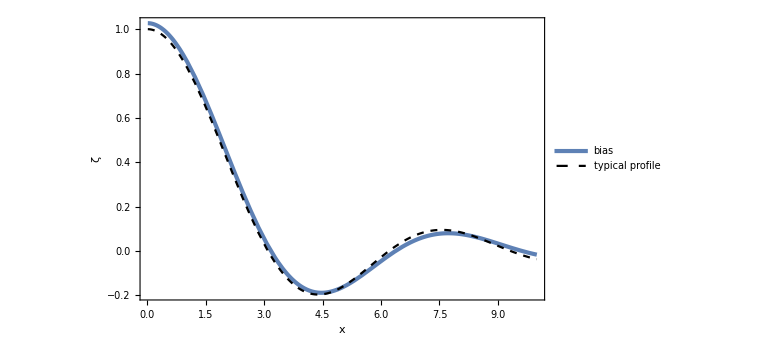

```mathematica
Plot[{biasint[x],ζx[x,k3tb]},{x,10^-2,10},PlotStyle->{AbsoluteThickness[3],{Black,Dashed}},FrameLabel->{{ζ,None},{x,σ^2==0.01}},PlotLegends->Placed[{"bias","typical profile"},{0.7,0.8}]]
```

```mathematica
Lbcheck[x_]=biasint''[x]+2/x biasint'[x];
Lpkcheck[x_]=D[D[ζx[x,k3tb], x], x]+2/x D[ζx[x,k3tb], x];
```

```mathematica
LLbcheck[x_]=Lbcheck''[x]+2/x Lbcheck'[x];
LLpkcheck[x_]=Lpkcheck''[x]+2/x Lpkcheck'[x];
```

```mathematica
Lbcheck[10^-2]
Lpkcheck[10^-2]
```

-1.06182676570928745565914

-1.061826765750829093783

```mathematica
LLbcheck[10^-2]
LLpkcheck[10^-2]
```

2.346790694432081976

2.3467967738203415

```mathematica
Cpk[x_]=2/3(1-(1+x Sqrt[As] σ1^2/σ2 ν2 ζp[x,k3tb])^2)/.{As->5 10^-3,ν2->8};
Cbias[x_]=2/3(1-(1+x Sqrt[As] σ1^2/σ2 ν2 bpint[x])^2)/.{As->5 10^-3,ν2->8};
```

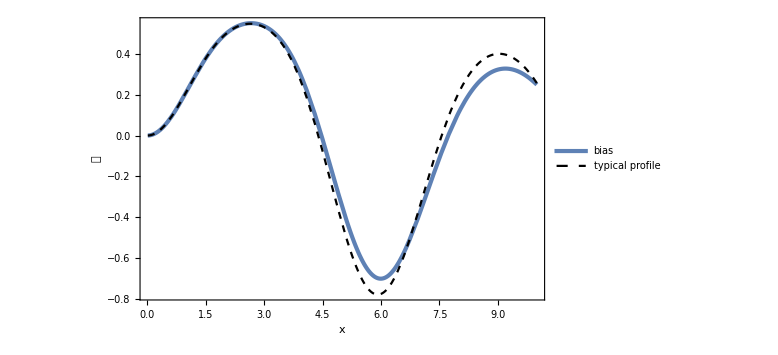

```mathematica
Plot[{Cbias[x],Cpk[x]},{x,10^-2,10},PlotStyle->{AbsoluteThickness[3],{Black,Dashed}},FrameLabel->{{𝒞,None},{x,σ^2==0.01}},PlotLegends->Placed[{"bias","typical profile"},{0.25,0.2}]]
```

## Lognormal σ^2=10^-1

```mathematica
npeak=16;
NL=256;
```

```mathematica
kpeak=2π npeak/NL
```

π/8

```mathematica
s2=10^-1;
```

```mathematica
σ1=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->1};
σ2=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->2};
σ3=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->3};
σ4=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->4};
```

```mathematica
calPz[lnk_]=1/Sqrt[2π s2] Exp[-lnk^2/(2s2)];
```

```mathematica
R3=Sqrt[3] σ3/σ4
```

(8 √3)/(ⅇ^(7/10) π)

```mathematica
R3//N
```

2.19025

```mathematica
γn=E^(-2s2)
```

1/ⅇ^(1/5)

```mathematica
ψ1[x_]:=kpeak^2/σ1^2 NIntegrate[E^(2lnk)calPz[lnk]Sinc[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2[x_]:=kpeak^4/σ2^2 NIntegrate[E^(4lnk)calPz[lnk]Sinc[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ1p[x_]:=kpeak^2/σ1^2 NIntegrate[E^(3lnk)calPz[lnk]Sinc'[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2p[x_]:=kpeak^4/σ2^2 NIntegrate[E^(5lnk)calPz[lnk]Sinc'[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
```

```mathematica
AbsoluteTiming[
ψ1List=ParallelTable[{x,ψ1[x]},{x,10^-2,10,10^-2}];
ψ1pList=ParallelTable[{x,ψ1p[x]},{x,10^-2,10,10^-2}];
ψ2List=ParallelTable[{x,ψ2[x]},{x,10^-2,10,10^-2}];
ψ2pList=ParallelTable[{x,ψ2p[x]},{x,10^-2,10,10^-2}];]
```

{12.9601,Null}

```mathematica
ψ1int[x_]=Interpolation[ψ1List][x];
ψ1pint[x_]=Interpolation[ψ1pList][x];
ψ2int[x_]=Interpolation[ψ2List][x];
ψ2pint[x_]=Interpolation[ψ2pList][x];
```

```mathematica
ζx[x_,k3t_]=(1/(1-γn^2)(ψ1int[x]-1/3 R3^2 σ2^2/σ1^2 ψ2int[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1int[x]-1/3 R3^2 σ2^2/σ1^2 ψ2int[x]));
ζp[x_,k3t_]=(1/(1-γn^2)(ψ1pint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2pint[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1pint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2pint[x]));
```

```mathematica
s2b=10^-1;
```

```mathematica
Normal[Series[Sinc''[E^lnk x]+2/(x E^lnk)Sinc'[E^lnk x],{x,0,0}]]
```

-1

```mathematica
1/x^2 D[(x^2 D[(b''[x]+2/x b'[x]), x]), x]//Simplify
```

(4 b^(3)[x])/x+b^(4)[x]

```mathematica
Normal[Series[Sinc''''[E^lnk x]+4/(x E^lnk)Sinc'''[E^lnk x],{x,0,0}]]
```

1

```mathematica
Lapb0=-kpeak^2 NIntegrate[E^(2lnk)1/Sqrt[2π s2b] Exp[-lnk^2/(2s2b)]Sqrt[calPz[lnk]],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
LapLapb0=kpeak^4 NIntegrate[E^(4lnk)1/Sqrt[2π s2b] Exp[-lnk^2/(2s2b)]Sqrt[calPz[lnk]],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
k3tb=Sqrt[σ2/σ4]Sqrt[-LapLapb0/Lapb0]
```

-0.161597674133744942791483575238

0.0371768569093574033209316104054

0.67032004603563930074443292515

-0.161597674133744942791483575238

0.0371768569093574033209316104054

0.67032004603563930074443292515

```mathematica
bias[x_]:=(-σ1^2/σ2^2 Lapb0)^-1 NIntegrate[Sinc[E^lnk x] 1/Sqrt[2π s2b] Exp[-lnk^2/(2s2b)]Sqrt[calPz[lnk]],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
bp[x_]:=(-σ1^2/σ2^2 Lapb0)^-1 NIntegrate[E^lnk Sinc'[E^lnk x] 1/Sqrt[2π s2b] Exp[-lnk^2/(2s2b)]Sqrt[calPz[lnk]],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
```

```mathematica
AbsoluteTiming[biasList=ParallelTable[{x,bias[x]},{x,10^-2,10,10^-2}];
bpList=ParallelTable[{x,bp[x]},{x,10^-2,10,10^-2}];]
```

{3.67671,Null}

```mathematica
biasint[x_]=Interpolation[biasList][x];
bpint[x_]=Interpolation[bpList][x];
```

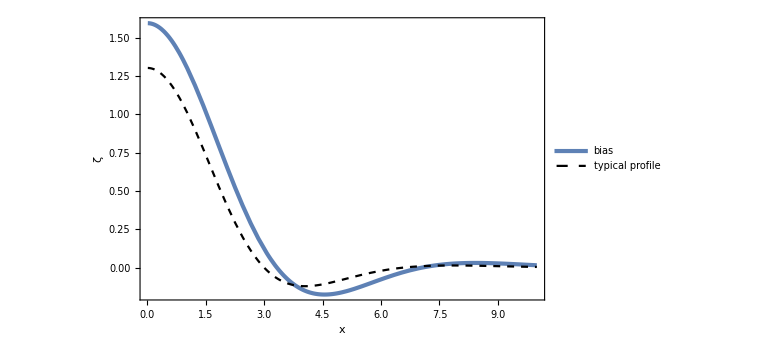

```mathematica
Plot[{biasint[x],ζx[x,k3tb]},{x,10^-2,10},PlotStyle->{AbsoluteThickness[3],{Black,Dashed}},FrameLabel->{{ζ,None},{x,σ^2==0.1}},PlotLegends->Placed[{"bias","typical profile"},{0.7,0.8}]]
```

```mathematica
Lbcheck[x_]=biasint''[x]+2/x biasint'[x];
Lpkcheck[x_]=D[D[ζx[x,k3tb], x], x]+2/x D[ζx[x,k3tb], x];
```

```mathematica
LLbcheck[x_]=Lbcheck''[x]+2/x Lbcheck'[x];
LLpkcheck[x_]=Lpkcheck''[x]+2/x Lpkcheck'[x];
```

```mathematica
Lbcheck[10^-2]
Lpkcheck[10^-2]
```

-1.82209614201266020946951

-1.8220961508792434790528

```mathematica
LLbcheck[10^-2]
LLpkcheck[10^-2]
```

5.435681311094415513

5.436978998701751013

```mathematica
Cpk[x_]=2/3(1-(1+x Sqrt[As] σ1^2/σ2 ν2 ζp[x,k3tb])^2)/.{As->5 10^-3,ν2->8};
Cbias[x_]=2/3(1-(1+x Sqrt[As] σ1^2/σ2 ν2 bpint[x])^2)/.{As->5 10^-3,ν2->8};
```

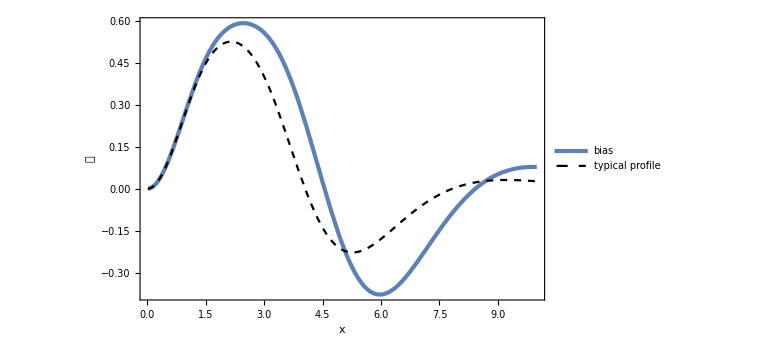

```mathematica
Plot[{Cbias[x],Cpk[x]},{x,10^-2,10},PlotStyle->{AbsoluteThickness[3],{Black,Dashed}},FrameLabel->{{𝒞,None},{x,σ^2==0.1}},PlotLegends->Placed[{"bias","typical profile"},{0.7,0.8}]]
```

## Lognormal σ^2=10^-1 kUV

```mathematica
npeak=16;
NL=256;
```

```mathematica
kpeak=2π npeak/NL
```

π/8

```mathematica
s2=10^-1;
s2b=10^-1;
```

```mathematica
calPz[lnk_]=1/Sqrt[2π s2] Exp[-lnk^2/(2s2)];
```

```mathematica
Lapb0=-kpeak^2 NIntegrate[E^(2lnk)1/Sqrt[2π s2b] Exp[-lnk^2/(2s2b)]Sqrt[calPz[lnk]],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30];
LapLapb0=kpeak^4 NIntegrate[E^(4lnk)1/Sqrt[2π s2b] Exp[-lnk^2/(2s2b)]Sqrt[calPz[lnk]],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30];
```

```mathematica
CList=ParallelTable[kUV=10^lnkUV kpeak;
σ1=kpeak Sqrt[NIntegrate[E^(2 lnk)calPz[lnk],{lnk,-∞,Log[kUV/kpeak]},Method->"GaussKronrodRule",WorkingPrecision->30]//Quiet];
σ2=kpeak^2 Sqrt[NIntegrate[E^(4 lnk)calPz[lnk],{lnk,-∞,Log[kUV/kpeak]},Method->"GaussKronrodRule",WorkingPrecision->30]//Quiet];
σ3=kpeak^3 Sqrt[NIntegrate[E^(6 lnk)calPz[lnk],{lnk,-∞,Log[kUV/kpeak]},Method->"GaussKronrodRule",WorkingPrecision->30]//Quiet];
σ4=kpeak^4 Sqrt[NIntegrate[E^(8 lnk)calPz[lnk],{lnk,-∞,Log[kUV/kpeak]},Method->"GaussKronrodRule",WorkingPrecision->30]//Quiet];
R3=Sqrt[3] σ3/σ4;
γ3=σ3^2/(σ2 σ4);
ψ1[x_]:=kpeak^2/σ1^2 NIntegrate[E^(2lnk)calPz[lnk]Sinc[E^lnk x],{lnk,-∞,Log[kUV/kpeak]},Method->"GaussKronrodRule",WorkingPrecision->30];
ψ2[x_]:=kpeak^4/σ2^2 NIntegrate[E^(4lnk)calPz[lnk]Sinc[E^lnk x],{lnk,-∞,Log[kUV/kpeak]},Method->"GaussKronrodRule",WorkingPrecision->30];
ψ1p[x_]:=kpeak^2/σ1^2 NIntegrate[E^(3lnk)calPz[lnk]Sinc'[E^lnk x],{lnk,-∞,Log[kUV/kpeak]},Method->"GaussKronrodRule",WorkingPrecision->30];
ψ2p[x_]:=kpeak^4/σ2^2 NIntegrate[E^(5lnk)calPz[lnk]Sinc'[E^lnk x],{lnk,-∞,Log[kUV/kpeak]},Method->"GaussKronrodRule",WorkingPrecision->30];
ψ1List=Table[{x,ψ1[x]},{x,10^-2,10,10^-2}];
ψ1pList=Table[{x,ψ1p[x]},{x,10^-2,10,10^-2}];
ψ2List=Table[{x,ψ2[x]},{x,10^-2,10,10^-2}];
ψ2pList=Table[{x,ψ2p[x]},{x,10^-2,10,10^-2}];
ψ1int[x_]=Interpolation[ψ1List][x];
ψ1pint[x_]=Interpolation[ψ1pList][x];
ψ2int[x_]=Interpolation[ψ2List][x];
ψ2pint[x_]=Interpolation[ψ2pList][x];
ζx[x_,k3t_]=(1/(1-γ3^2)(ψ1int[x]-1/3 R3^2 σ2^2/σ1^2 ψ2int[x])-k3t^2/(γ3(1-γ3^2))(γ3^2 ψ1int[x]-1/3 R3^2 σ2^2/σ1^2 ψ2int[x]));
ζp[x_,k3t_]=(1/(1-γ3^2)(ψ1pint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2pint[x])-k3t^2/(γ3(1-γ3^2))(γ3^2 ψ1pint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2pint[x]));
k3tb=Sqrt[σ2/σ4]Sqrt[-LapLapb0/Lapb0];
bias[x_]:=(-σ1^2/σ2^2 Lapb0)^-1 NIntegrate[Sinc[E^lnk x] 1/Sqrt[2π s2b] Exp[-lnk^2/(2s2b)]Sqrt[calPz[lnk]],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30];
bp[x_]:=(-σ1^2/σ2^2 Lapb0)^-1 NIntegrate[E^lnk Sinc'[E^lnk x] 1/Sqrt[2π s2b] Exp[-lnk^2/(2s2b)]Sqrt[calPz[lnk]],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30];
biasList=Table[{x,bias[x]},{x,10^-2,10,10^-2}];
bpList=Table[{x,bp[x]},{x,10^-2,10,10^-2}];
biasint[x_]=Interpolation[biasList][x];
bpint[x_]=Interpolation[bpList][x];
Cpk[x_]=2/3(1-(1+x Sqrt[As] σ1^2/σ2 ν2 ζp[x,k3tb])^2)/.{As->5 10^-3,ν2->8};
Cbias[x_]=2/3(1-(1+x Sqrt[As] σ1^2/σ2 ν2 bpint[x])^2)/.{As->5 10^-3,ν2->8};
{Cpk[x],Cbias[x]},{lnkUV,0,1,10^-1}];//AbsoluteTiming
```

{128.668,Null}

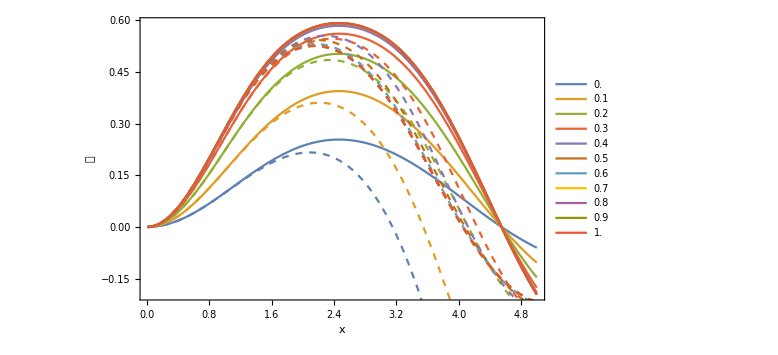

```mathematica
FigC=Show[Plot[Evaluate[CList[[All,2]]],{x,10^-2,5},PlotStyle->Automatic,FrameLabel->{{𝒞,None},{x,"log_10(k_UV/k_*) = ??"}},PlotLegends->LineLegend[Table[ToString[lnkUV//N],{lnkUV,0,1,10^-1}],LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"],LegendLayout->{"Column",2}]],Plot[Evaluate[CList[[All,1]]],{x,10^-2,5},PlotStyle->Dashed]]
```

```mathematica
Export["C_biasvskUV.pdf",FigC]
```

C_biasvskUV.pdf

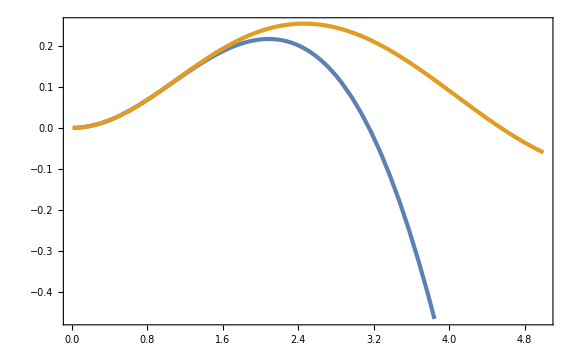
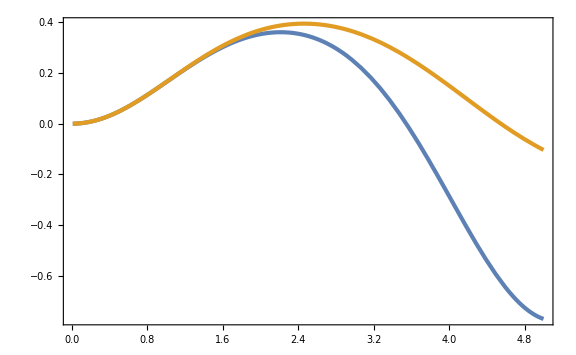
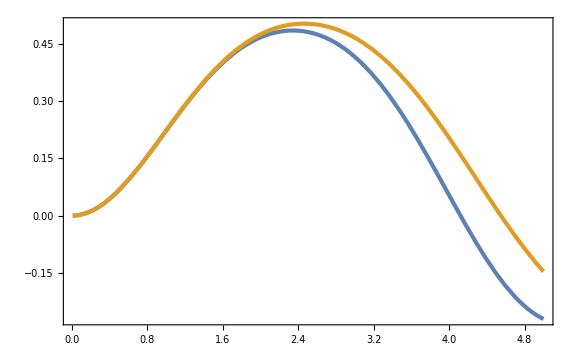
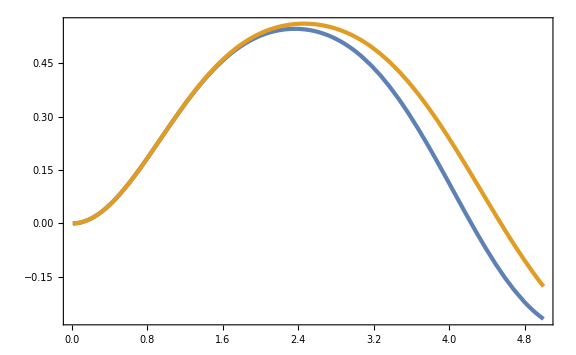
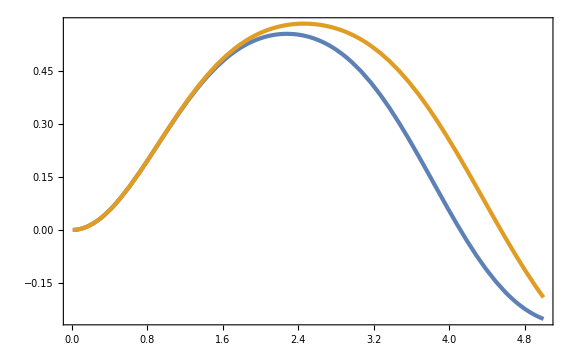
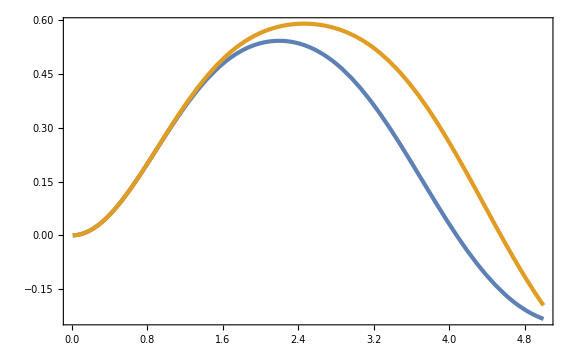
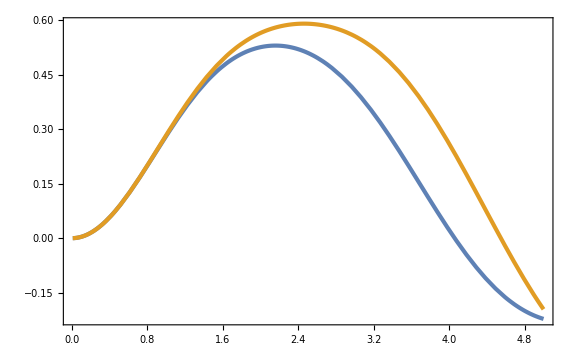
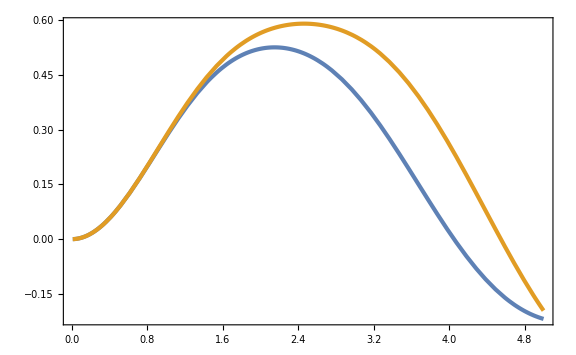

```mathematica
Table[Plot[Evaluate[CList[[i]]],{x,10^-2,5}],{i,Length[CList]}]
```

## Lognormal σ^2=10^-1: dominant profile (MPP)

σ.b2=0.1, A_s=5×10⁻.b3 の total f_PBH に最も効く profile (dominant profile) を MPP (most probable point) 探索で求め、現在の bias・typical profile と比較する。f_PBH ∝ E_p[ M(x)·1[C_max(x)>C_th] ] で、希少事象なので Gaussian 測度 p のもとで ln M(x) − |x|.b2/2 を最大にする点が支配的 (ν₂≈5〜9 では指数部が 30〜50 あり、多項式の前因子は無視)。球対称部分 ζ̄(x) (x=k_peak r) を lnk 方向に離散化したモード振幅 u_i~N(0,1) で ζ̄(x)=Σ A_i(x)u_i, v(x)=xζ̄′(x)=Σ B_i(x)u_i (どちらも u に線形) と書く。C=⅔(1−(1+v).b2) なので C_max>C_th ⇔ ある x* で v(x*)≤v_th=−1+√(1−3C_th/2)。x* を固定すると拘束は線形で、最小コストは v_th.b2/(2Var v(x*)) (閉じた形)、最適 profile は ζ̄ と v(x*) の共分散に比例する。質量重み M=x_m.b2 e^{2ζ_m}(C_max−C_th)^γ (γ=0.36) を含めると、最適な u は {B(x*), A(x*), ∂ₓB(x*)} の張る 3 次元空間にあるので、その中で J=ln M−|u|.b2/2 を最大化する。ν₂=μ₂/σ₂, k̃₃ は u の ∇.b2ζ, ∇⁴ζ 成分 (L₂, L₄) から読む。

```mathematica
s2m=1/10;kpm=π/8;Asm=1/200;Cthm=0.533;gamm=0.36;sig[n_]:=√(Exp[2 n^2 s2m] kpm^(2 n));dl=0.01;lk=Range[-2.5,2.5,dl];Pz=PDF[NormalDistribution[0,√s2m],lk];sq=√(Asm Pz dl);xs=Range[0.01,12,0.01];SincT[u_]:=Sin[u]/u;DSinc[u_]:=Cos[u]/u-Sin[u]/u^2;Amat=Table[sq SincT[Exp[lk] x],{x,xs}];Bmat=Table[sq Exp[lk] x DSinc[Exp[lk] x],{x,xs}];vth=-1+√(1-1.5 Cthm);{Total[sq^2],vth}
```

{0.005,-0.552228}

```mathematica
$Failed
```

$Failed

```mathematica
logM[u_]:=Module[{c,xm,i,cc},{c,xm,i}=cmax[u];cc=c-Cthm;2 Log[xm]+2 Amat⟦i⟧.u+If[cc>1/10^6,gamm Log[cc],gamm Log[1/10^6]+300 (cc-1/10^6)]];Jf[u_]:=logM[u]-(u.u)/2;bestAt[i_]:=Module[{a=Amat⟦i⟧,b=Bmat⟦i⟧,d=Bmat⟦Min[i+1,Length[xs]]⟧-Bmat⟦Max[i-1,1]⟧,al,be,ga,r},r=Quiet[FindMaximum[Jf[al b+be a+ga d],{{al,(1.05 vth)/varv⟦i⟧},{be,0.},{ga,0.}},MaxIterations->300]];{r⟦1⟧,al b+be a+ga d/.r⟦2⟧}];
```

```mathematica
L2[u_]:=kpm^2 Total[Exp[2 lk] √(Pz dl) u];L4[u_]:=kpm^4 Total[Exp[4 lk] √(Pz dl) u];nuK[u_]:={L2[u]/sig[2],√Abs[(sig[2] L4[u])/(sig[4] L2[u])]};Eg={kpm^2 Exp[2 lk] √(Pz dl),kpm^4 Exp[4 lk] √(Pz dl)};utyp[nu_,k3_]:=Transpose[Eg].LinearSolve[Eg.Transpose[Eg],{nu sig[2],k3^2 nu sig[4]}];ubias0=√dl PDF[NormalDistribution[0,√s2m],lk];{nuK[uMPP],nuK[uTh],nuK[ubias0]}
```

{{5.5232,0.488867},{5.44522,0.543701},{0.702421,0.67032}}

```mathematica
ixList=Range[40,700,20];scan=Table[Module[{r=bestAt[i]},{xs⟦i⟧,r⟦1⟧}],{i,ixList}];ib0=ixList⟦First[Ordering[scan⟦All,2⟧,-1]]⟧;ixList2=Range[Max[ib0-20,10],ib0+20,4];scan2=Table[Module[{r=bestAt[i]},{xs⟦i⟧,r⟦1⟧}],{i,ixList2}];ibest=ixList2⟦First[Ordering[scan2⟦All,2⟧,-1]]⟧;rbest=bestAt[ibest];uMPP=rbest⟦2⟧;{ibest,xs⟦ibest⟧,rbest⟦1⟧,cmax[uMPP],nuK[uMPP],logM[uMPP],(uMPP.uMPP)/2}
```

{152,1.52,-40.2894,{0.534742,2.52,252},{5.5232,0.488867},-0.136278,40.1093}

```mathematica
tg=Flatten[Table[{nn,kk,Jf[utyp[nn,kk]]},{nn,5.5,10.,0.1},{kk,0.35,1.,0.025}],1];rtyp=tg⟦First[Ordering[tg⟦All,3⟧,-1]]⟧;uTypOpt=utyp[rtyp⟦1⟧,rtyp⟦2⟧];tgrid=(Range[0.5,3.,0.02] vth)/(Bmat⟦ix0⟧.ubias0);tJ=Table[{t,Jf[t ubias0]},{t,tgrid}];uBiasOpt=tJ⟦First[Ordering[tJ⟦All,2⟧,-1]],1⟧ ubias0;tBias=uBiasOpt⟦251⟧/ubias0⟦251⟧;nkM=nuK[uMPP];uTypSame=utyp[nkM⟦1⟧,nkM⟦2⟧];summ[name_,u_]:=Module[{cm=cmax[u]},{name,(u.u)/2,logM[u],Jf[u],nuK[u],cm⟦1⟧,cm⟦2⟧}];tab={summ["MPP (mass-weighted)",uMPP],summ["MPP (C=Cth only)",uTh],summ["current bias (optimal amplitude)",uBiasOpt],summ["typical (best nu2,k3t)",uTypOpt],summ["typical @ (nu2,k3t) of MPP",uTypSame]};{{({#1⟦1⟧,Slot["1"]⟦"2"⟧,Slot["1"]⟦"3"⟧,Slot["1"]⟦"4"⟧,Round[#1⟦5⟧,0.001],Slot["1"]⟦"6"⟧,#1⟦7⟧}&)/@tab}, {"bias coefficient bc of the optimal amplitude: "tBias}}
```

{{MPP (mass-weighted),40.1093,-0.136278,-40.2456,{5.523,0.489},0.534742,2.52},{MPP (C=Cth only),38.8023,-2.81739,-41.6197,{5.445,0.544},0.533,2.57},{current bias (optimal amplitude),40.4967,-0.23989,-40.7366,{6.693,0.67},0.534475,2.46},{typical (best nu2,k3t),48.2203,-0.31723,-48.5375,{8.3,0.675},0.535383,2.14},{typical @ (nu2,k3t) of MPP,30.8027,-26.3965,-57.1992,{5.523,0.489},0.455447,2.22}}
bias coefficient bc of the optimal amplitude: 9.52856

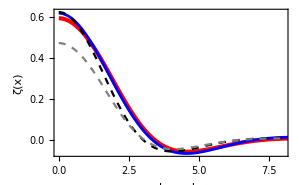
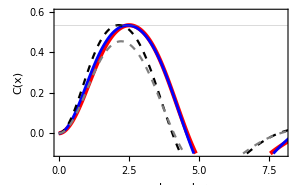

```mathematica
profs={uMPP,uBiasOpt,uTypOpt,uTypSame};leg={"MPP","current bias","typical (best)","typical @ MPP (nu2,k3t)"};sty={Directive[Red,AbsoluteThickness[3]],Directive[Blue,AbsoluteThickness[2]],Directive[Black,Dashed],Directive[Gray,Dashed]};pz=ListLinePlot[Table[Transpose[{xs,Amat.u}],{u,profs}],PlotRange->{{0,8},All},PlotStyle->sty,Frame->True,FrameLabel->{"x = k_peak r","ζ(x)"},ImageSize->300];pc=ListLinePlot[Table[Transpose[{xs,Cof[u]}],{u,profs}],PlotRange->{{0,8},{-0.1,0.6}},PlotStyle->sty,Frame->True,FrameLabel->{"x = k_peak r","C(x)"},GridLines->{None,{Cthm}},ImageSize->300];pzpcLineLegend[sty,leg]
```

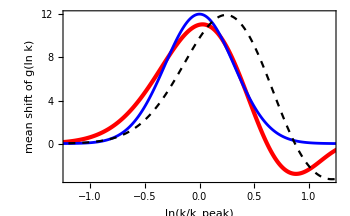

```mathematica
ListLinePlot[Table[Transpose[{lk,u/(√dl)}],{u,{uMPP,uBiasOpt,uTypOpt}}],PlotRange->{{-1.2,1.2},All},PlotStyle->sty⟦1;;3⟧,Frame->True,FrameLabel->{"ln(k/k_peak)","mean shift of g(ln k)"},ImageSize->350]LineLegend[sty⟦1;;3⟧,leg⟦1;;3⟧]
```

```mathematica
{"|u_MPP-u_bias|^2"->(uMPP-uBiasOpt).(uMPP-uBiasOpt),"cos(u_MPP,u_bias)"->(uMPP.uBiasOpt)/(Norm[uMPP] Norm[uBiasOpt]),"|u_MPP-u_typ(best)|^2"->(uMPP-uTypOpt).(uMPP-uTypOpt),"Delta C of MPP vs typical at same (nu2,k3t)"->cmax[uMPP]⟦1⟧-cmax[uTypSame]⟦1⟧}
```

{|u_MPP-u_bias|^2→4.87261,cos(u_MPP,u_bias)→0.969786,|u_MPP-u_typ(best)|^2→26.4313,Delta C of MPP vs typical at same (nu2,k3t)→0.0792945}

結果 (J=ln M−|u|.b2/2 は −（その profile に到達するための指数コスト）に ln M を加えたもの): MPP は J=−40.2 (ν₂=5.5, k̃₃=0.49, C_max=0.535, x_m=2.5)、現在の bias は最適振幅で J=−40.7 (ν₂=6.7, k̃₃=0.67)、typical profile の最良点は J=−48.5 (ν₂=8.3, k̃₃=0.68)。bias の最適振幅は bc=9.53 で、実際に使っている bc=9.5 とほぼ一致する (bc の単位は mean shift の係数)。dominant profile は typical より J が約 8 大きく (e⁸≈3000; 実測 IS/PT≈300 は前因子・揺らぎを含めた値)、現在の bias は MPP と J が 0.5 しか違わない。ζ(x), C(x) の形も bias と MPP はほぼ重なり (cos(u_MPP,u_bias)=0.97, |u_MPP−u_bias|.b2=4.9)、typical とは明確に違う (|u_MPP−u_typ|.b2=26)。したがって bias は dominant profile のよい近似になっている。ただし MPP は bias より ν₂, k̃₃ が小さく (5.5, 0.49)、その (ν₂, k̃₃) の typical profile より C_max が +0.079 大きい。これは lattice で測った ΔC の散らばり (sd≈0.017–0.020) の約 4σ に相当し、畳み込み PT で寄与が集中した ΔC/σ≈3.5 とも整合する。前因子 (ν₂ の多項式、peak 判定の Jacobian) と MPP まわりの揺らぎは含めていない。